```mathematica
(* Kallan Berglund *)
```

# Solving for P_2dot, setting second order to zero and solving for unknowns like dN’

```mathematica
(*     Quit[]   *)
```

## Definitions

### Enforcing static condition

```mathematica
Subscript[p, 2][x_]:=0;
Subscript[p, 3][x_]:=0;
```

### Defining Initial Lapse Function and Classical Hamiltonian

```mathematica
Subscript[N, 0]=Sqrt[1-2M/x];
Subscript[H, integrand]=-n[x]*(Subscript[ϕ, 2][x]*Subscript[p, 2][x]^2/2/Sqrt[Subscript[ϕ, 1][x]]+2Sqrt[Subscript[ϕ, 1][x]]*Subscript[p, 1][x]*Subscript[p, 2][x]+(1-(D[Subscript[ϕ, 1][x],x]/Subscript[ϕ, 2][x])^2)Subscript[ϕ, 2][x]/2/Sqrt[Subscript[ϕ, 1][x]]-2D[D[Subscript[ϕ, 1][x],x]/Subscript[ϕ, 2][x],x]Sqrt[Subscript[ϕ, 1][x]]);
```

### Defining Hamiltonian, Modifications, and Derivatives

```mathematica
dHdϕ2=D[Subscript[H, integrand],Subscript[ϕ, 2][x]];
dHdϕ2prime=-n[x] (-2 √(Subscript[ϕ, 1][x]) (-D[Subscript[ϕ, 1][x],x]/(Subscript[ϕ, 2][x])^2));
Subscript[H, Subscript[2, integrand]]=n[x](Subscript[ϕ, 2][x] Subscript[p, 3][x]^2/(2Sqrt[Subscript[ϕ, 1][x]])+Subscript[ϕ, 3][x] Subscript[p, 2][x] Subscript[p, 3][x]/Sqrt[Subscript[ϕ, 1][x]]+Subscript[ϕ, 3][x]^2(6Sqrt[Subscript[ϕ, 1][x]] D[Subscript[ϕ, 1][x],x]D[Subscript[ϕ, 2][x],x]/Subscript[ϕ, 2][x]^4-D[Subscript[ϕ, 1][x],x]^2/(2Sqrt[Subscript[ϕ, 1][x]]Subscript[ϕ, 2][x]^3)-2D[D[Subscript[ϕ, 1][x],x],x]Sqrt[Subscript[ϕ, 1][x]]/Subscript[ϕ, 2][x]^3)-4Sqrt[Subscript[ϕ, 1][x]]D[Subscript[ϕ, 1][x],x]Subscript[ϕ, 3][x] D[Subscript[ϕ, 3][x],x]/Subscript[ϕ, 2][x]^3+U[x] Subscript[ϕ, 2][x]/(2Sqrt[Subscript[ϕ, 1][x]]Subscript[ϕ, 3][x]^2));
dH2dϕ2=D[Subscript[H, Subscript[2, integrand]],Subscript[ϕ, 2][x]];
dH2dϕ2prime=D[Subscript[H, Subscript[2, integrand]],D[Subscript[ϕ, 2][x],x]];
```

### Defining initial/static conditions and tracking order of terms

```mathematica
Subscript[ϕ, 1][x_]:= x^2;
Subscript[ϕ, 2][x_]:=2x/Sqrt[1-2M/x]+Subscript[dϕ, 2] [x]*order;
Subscript[ϕ, 3][x_]:= Subscript[ϕ, Subscript[3, 0]][x]*order;
n[x_]:=Sqrt[1-2M/x]+dN[x]*order;
U[x_]:= u[x]*order^4;
Subscript[p, 3][x_]:=Subscript[P, 3][x]*order;
```

## Calculating p2dot

### Calculating p_2dot

```mathematica
p2dot=FullSimplify[-dHdϕ2+D[dHdϕ2prime,x]-Subscript[N, 0] dH2dϕ2+D[Subscript[N, 0] dH2dϕ2prime,x] ,x>0];
Taylorp2dot=Series[p2dot,{order,0,2}]
```

((32 M x^6 dN[x]-16 (2 M-x) x^5 dϕ_2[x]-32 x^7 (-2 M+x) dN'[x]) order)/(32 x^8)+1/(2 x^4 (ϕ_(3_0)[x])^2)(-(√(1-(2 M)/x) dϕ_2[x] (ϕ_(3_0)[x])^2 (32 M x^6 dN[x]-16 (2 M-x) x^5 dϕ_2[x]-32 x^7 (-2 M+x) dN'[x]))/(8 x^5)+1/(16 x^4)(16 (2 M-x) x^6 u[x]+(ϕ_(3_0)[x])^2 (16 x^(9/2) √(-2 M+x) (2 M+x) dN[x] dϕ_2[x]+20 x^(7/2) (-2 M+x)^(3/2) dϕ_2[x]^2+12 (2 M-x)^2 x^2 (2 M+x) (ϕ_(3_0)[x])^2+32 (2 M-x) x^5 √(x (-2 M+x)) dϕ_2[x] dN'[x]))) order^2+O[order]^3

```mathematica
p2dotFirstOrder=SeriesCoefficient[Taylorp2dot, 1]
p2dotSecondOrder=SeriesCoefficient[Taylorp2dot, 2]
```

(32 M x^6 dN[x]-16 (2 M-x) x^5 dϕ_2[x]-32 x^7 (-2 M+x) dN'[x])/(32 x^8)

1/(2 x^4 (ϕ_(3_0)[x])^2)(-(√(1-(2 M)/x) dϕ_2[x] (ϕ_(3_0)[x])^2 (32 M x^6 dN[x]-16 (2 M-x) x^5 dϕ_2[x]-32 x^7 (-2 M+x) dN'[x]))/(8 x^5)+1/(16 x^4)(16 (2 M-x) x^6 u[x]+(ϕ_(3_0)[x])^2 (16 x^(9/2) √(-2 M+x) (2 M+x) dN[x] dϕ_2[x]+20 x^(7/2) (-2 M+x)^(3/2) dϕ_2[x]^2+12 (2 M-x)^2 x^2 (2 M+x) (ϕ_(3_0)[x])^2+32 (2 M-x) x^5 √(x (-2 M+x)) dϕ_2[x] dN'[x])))

## Solve for dN

### Replace dN' using equation 64

```mathematica
(* Solve eq 64 for Subscript[dϕ, 2], plug in, then solve for dN *)
Solve[0==(1-2M/x)^(3/2)(-1/(2x^2Sqrt[1-2M/x])Subscript[dϕ, 2][x]+D[dN[x]/Sqrt[1-2M/x],x]),dN'[x]]
```

{{dN'[x]→(-2 M x dN[x]+2 M dϕ_2[x]-x dϕ_2[x])/(2 (2 M-x) x^2)}}

```mathematica
dN'[x]:=(-2 M x dN[x]+2 M Subscript[dϕ, 2][x]-x Subscript[dϕ, 2][x])/(2 (2 M-x) x^2)
```

### Set second order term from p2dot to zero and solve for dN

```mathematica
DN=Solve[0==p2dotSecondOrder,dN[x]][[1]][[1]]
```

dN[x]→((√(1-(2 M)/x) (2 M-x) dϕ_2[x]^2)/x^4+(2 M √(1-(2 M)/x) (-2 M+x) dϕ_2[x]^2)/((2 M-x) x^4)-(√(1-(2 M)/x) (-2 M+x) dϕ_2[x]^2)/((2 M-x) x^3)+(5 (-2 M+x)^(3/2) dϕ_2[x]^2)/(8 x^(9/2))+(M √(x (-2 M+x)) dϕ_2[x]^2)/x^5-(√(x (-2 M+x)) dϕ_2[x]^2)/(2 x^4)+((2 M-x) u[x])/(2 x^2 (ϕ_(3_0)[x])^2)+(3 (2 M-x)^2 (2 M+x) (ϕ_(3_0)[x])^2)/(8 x^6))/((2 M √(1-(2 M)/x) dϕ_2[x])/x^3+(2 M √(1-(2 M)/x) (-2 M+x) dϕ_2[x])/((2 M-x) x^3)+(M √(x (-2 M+x)) dϕ_2[x])/x^4-(√(-2 M+x) (2 M+x) dϕ_2[x])/(2 x^(7/2)))

```mathematica
(* Simplify (FullSimplify yields the same) *)
Simplify[DN]
```

dN[x]→((-2 M+x) (4 x^4 u[x]+x (-5 √x √(-2 M+x)+4 √(x (-2 M+x))) dϕ_2[x]^2 (ϕ_(3_0)[x])^2+3 (4 M^2-x^2) (ϕ_(3_0)[x])^4))/(4 x^2 (2 M √x √(-2 M+x)+x^(3/2) √(-2 M+x)-2 M √(x (-2 M+x))) dϕ_2[x] (ϕ_(3_0)[x])^2)

```mathematica
(* Manually simplified dN[x] (corrected) *)
dNofx=dN[x]-> Sqrt[-2M+x]/(4 x^(7/2) Subscript[dϕ, 2][x] (Subscript[ϕ, Subscript[3, 0]][x])^2)(4 x^4 u[x]-x^(3/2) Sqrt[-2M+x] (Subscript[dϕ, 2][x])^2 (Subscript[ϕ, Subscript[3, 0]][x])^2+3(2M+x)(2M-x) (Subscript[ϕ, Subscript[3, 0]][x])^4)
```

dN[x]→(√(-2 M+x) (4 x^4 u[x]-x^(3/2) √(-2 M+x) dϕ_2[x]^2 (ϕ_(3_0)[x])^2+3 (2 M-x) (2 M+x) (ϕ_(3_0)[x])^4))/(4 x^(7/2) dϕ_2[x] (ϕ_(3_0)[x])^2)

## Calculating constraint equation for u[x]

### Subbing in to create constraint equation for u[x]

```mathematica
(* Sub dN back into equation 64 and see how solving for U isn't productive here *)
Simplify [0==(1-2M/x)^(3/2)(-1/(2x^2Sqrt[1-2M/x])Subscript[dϕ, 2][x]+D[dN[x]/Sqrt[1-2M/x]/. dNofx,x]) ]
DSolve[0==(1-2M/x)^(3/2)(-1/(2x^2Sqrt[1-2M/x])Subscript[dϕ, 2][x]+D[dN[x]/Sqrt[1-2M/x]/. dNofx,x]) , u[x],x]
```

1/(√x dϕ_2[x] ϕ_(3_0)[x])√(-2 M+x) (x^(3/2) √(-2 M+x) (3 M+x) dϕ_2[x]^3 (ϕ_(3_0)[x])^3+x^(5/2) (-2 M+x)^(3/2) dϕ_2[x]^2 (ϕ_(3_0)[x])^3 dϕ_2'[x]-3 x (-2 M+x)^2 (2 M+x) (ϕ_(3_0)[x])^5 dϕ_2'[x]+(2 M-x) dϕ_2[x] ϕ_(3_0)[x] ((-36 M^2+3 x^2) (ϕ_(3_0)[x])^4+4 x^5 u'[x]-6 x (-4 M^2+x^2) (ϕ_(3_0)[x])^3 ϕ_(3_0)'[x])-4 (2 M-x) x^4 u[x] (x ϕ_(3_0)[x] dϕ_2'[x]-dϕ_2[x] (ϕ_(3_0)[x]-2 x ϕ_(3_0)'[x])))==0

{{u[x]→(C[1] dϕ_2[x] (ϕ_(3_0)[x])^2)/x+1/x(3 M K[1]^(3/2) √(-2 M+K[1]) dϕ_2[K[1]]^3 (ϕ_(3_0)[K[1]])^3+K[1]^(5/2) √(-2 M+K[1]) dϕ_2[K[1]]^3 (ϕ_(3_0)[K[1]])^3-72 M^3 dϕ_2[K[1]] (ϕ_(3_0)[K[1]])^5+36 M^2 K[1] dϕ_2[K[1]] (ϕ_(3_0)[K[1]])^5+6 M K[1]^2 dϕ_2[K[1]] (ϕ_(3_0)[K[1]])^5-3 K[1]^3 dϕ_2[K[1]] (ϕ_(3_0)[K[1]])^5-2 M K[1]^(5/2) √(-2 M+K[1]) dϕ_2[K[1]]^2 (ϕ_(3_0)[K[1]])^3 dϕ_2'[K[1]]+K[1]^(7/2) √(-2 M+K[1]) dϕ_2[K[1]]^2 (ϕ_(3_0)[K[1]])^3 dϕ_2'[K[1]]-24 M^3 K[1] (ϕ_(3_0)[K[1]])^5 dϕ_2'[K[1]]+12 M^2 K[1]^2 (ϕ_(3_0)[K[1]])^5 dϕ_2'[K[1]]+6 M K[1]^3 (ϕ_(3_0)[K[1]])^5 dϕ_2'[K[1]]-3 K[1]^4 (ϕ_(3_0)[K[1]])^5 dϕ_2'[K[1]]+48 M^3 K[1] dϕ_2[K[1]] (ϕ_(3_0)[K[1]])^4 ϕ_(3_0)'[K[1]]-24 M^2 K[1]^2 dϕ_2[K[1]] (ϕ_(3_0)[K[1]])^4 ϕ_(3_0)'[K[1]]-12 M K[1]^3 dϕ_2[K[1]] (ϕ_(3_0)[K[1]])^4 ϕ_(3_0)'[K[1]]+6 K[1]^4 dϕ_2[K[1]] (ϕ_(3_0)[K[1]])^4 ϕ_(3_0)'[K[1]])/(4 K[1]^4 (-2 M+K[1]) dϕ_2[K[1]]^2 (ϕ_(3_0)[K[1]])^3)K[1]1x dϕ_2[x] (ϕ_(3_0)[x])^2}}

```mathematica
(* Sub Subscript[ϕ, Subscript[3, 0]][x] from eq 49 *)
Subscript[ϕ, Subscript[3, 0]][x_]:=c/(1-2M/x)^(3/2)
(* Sub Subscript[dϕ, 2][x] from eq 63 *)
Subscript[dϕ, 2][x_]:= Sqrt[e Sqrt[x]/(1-2M/x)^(5/2)-3 c^2/(1-2M/x)^3+2 Sqrt[x]/(c^2 (1-2M/x)^(5/2)) Integrate[u[x](x-2M)^(7/2)/x^3,x]]

Uconstraint=Simplify [0==(1-2M/x)^(3/2)(-1/(2x^2Sqrt[1-2M/x])Subscript[dϕ, 2][x]+D[dN[x]/Sqrt[1-2M/x]/. dNofx,x])]
```

(20 x^6 (-2 M+x)^(3/2) (∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx)^2+4 c^2 (2 M-x)^5 x^(3/2) (e √x (-2 M+x) (28 M √(1-(2 M)/x)+(-1+3 √(1-(2 M)/x)) x)+3 c^2 (56 M^2+(-4+√(1-(2 M)/x)) x^2+√(1-(2 M)/x) x^(3/2) √(-2 M+x)+M (-20 x+2 √(1-(2 M)/x) √x √(-2 M+x)))) u[x]+16 √(1-(2 M)/x) (-2 M+x)^(21/2) u[x]^2+c^2 x^(5/2) (432 c^6 M^3 x-144 c^4 e M^3 √(1-(2 M)/x) x^(3/2)-432 c^6 M^2 x^2+156 c^4 e M^2 √(1-(2 M)/x) x^(5/2)+36 c^6 M x^3-12 c^4 e M √(1-(2 M)/x) x^(7/2)+36 c^6 x^4-15 c^4 e √(1-(2 M)/x) x^(9/2)+36 c^6 x^(7/2) √(-2 M+x)-10 c^2 e^2 M x^(7/2) √(-2 M+x)-27 c^4 e √(1-(2 M)/x) x^4 √(-2 M+x)+5 c^2 e^2 x^(9/2) √(-2 M+x)+16 (3 c^2-e √(1-(2 M)/x) √x) (-2 M+x)^7 u'[x])+(∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx) (20 c^2 e x^6 (-2 M+x)^(3/2)-6 c^4 √(1-(2 M)/x) x^4 (48 M^3-52 M^2 x+4 M x^2+5 x^3+9 x^(5/2) √(-2 M+x))-8 x^2 (-2 M+x)^6 (28 M √(1-(2 M)/x)+(-1+3 √(1-(2 M)/x)) x) u[x]-32 √(1-(2 M)/x) x^3 (-2 M+x)^7 u'[x]))/(√x √(-2 M+x) (-3 c^5+c^3 e √(1-(2 M)/x) √x+2 c √(1-(2 M)/x) √x ∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx) √((-3 c^4 x^3+c^2 e √(1-(2 M)/x) x^(7/2)+2 √(1-(2 M)/x) x^(7/2) ∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx)/(c^2 (-2 M+x)^3)))==0

### Ruling out simple options (can skip ahead)

```mathematica
(* Test whether u=0 is a solution (it's not)*)
SimplestCaseU0=Simplify[Uconstraint/. u[x]->0];
TrueQ[SimplestCaseU0]
```

False

```mathematica
(* Demonstrating that DSolve can't identify a function for u[x]*)
DSolve[Uconstraint,u[x],x]
```

DSolve[(20 x^6 (-2 M+x)^(3/2) (∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx)^2+4 c^2 (2 M-x)^5 x^(3/2) (e √x (-2 M+x) (28 M √(1-(2 M)/x)+(-1+3 √(1-(2 M)/x)) x)+3 c^2 (56 M^2+(-4+√(1-(2 M)/x)) x^2+√(1-(2 M)/x) x^(3/2) √(-2 M+x)+M (-20 x+2 √(1-(2 M)/x) √x √(-2 M+x)))) u[x]+16 √(1-(2 M)/x) (-2 M+x)^(21/2) u[x]^2+c^2 x^(5/2) (432 c^6 M^3 x-144 c^4 e M^3 √(1-(2 M)/x) x^(3/2)-432 c^6 M^2 x^2+156 c^4 e M^2 √(1-(2 M)/x) x^(5/2)+36 c^6 M x^3-12 c^4 e M √(1-(2 M)/x) x^(7/2)+36 c^6 x^4-15 c^4 e √(1-(2 M)/x) x^(9/2)+36 c^6 x^(7/2) √(-2 M+x)-10 c^2 e^2 M x^(7/2) √(-2 M+x)-27 c^4 e √(1-(2 M)/x) x^4 √(-2 M+x)+5 c^2 e^2 x^(9/2) √(-2 M+x)+16 (3 c^2-e √(1-(2 M)/x) √x) (-2 M+x)^7 u'[x])+(∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx) (20 c^2 e x^6 (-2 M+x)^(3/2)-6 c^4 √(1-(2 M)/x) x^4 (48 M^3-52 M^2 x+4 M x^2+5 x^3+9 x^(5/2) √(-2 M+x))-8 x^2 (-2 M+x)^6 (28 M √(1-(2 M)/x)+(-1+3 √(1-(2 M)/x)) x) u[x]-32 √(1-(2 M)/x) x^3 (-2 M+x)^7 u'[x]))/(√x √(-2 M+x) (-3 c^5+c^3 e √(1-(2 M)/x) √x+2 c √(1-(2 M)/x) √x ∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx) √((-3 c^4 x^3+c^2 e √(1-(2 M)/x) x^(7/2)+2 √(1-(2 M)/x) x^(7/2) ∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx)/(c^2 (-2 M+x)^3)))==0,u[x],x]

## Numerics

### Fixing constants, scaled by order or magnitude

```mathematica
(* Solve for U[x} numerically (need range of values for x and values for everyting else not yet fixed) *)
(* c is 1st order, e is 2nd order, u[x] is 4th order, so set c and e to 0.01^(order). Make M=1 and x start at 10 so the quantum effects are smaller than the curvature effects *)

constants={c->0.01, e->0.01^2, M->1}
```

{c→0.01,e→0.0001,M→1}

### Direct numerics produce result but also Mathematica errors---Skip to next section where squaring the constraint solves the Mathematica issues without changing the result

```mathematica
(* This section included in code for error reference, but can skip ahead to UconstraintSquared *)
```

ReplaceAll::reps: {uis1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

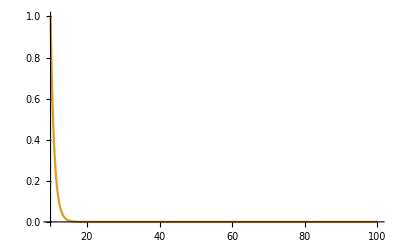

```mathematica
Plot[{u[x]/.uis1, E^(10-x)},{x,10,100}, PlotRange->All]
```

```mathematica
FirstTable=Table[NDSolve[{Uconstraint/. constants, u[10]==a}, u[x], {x,10, 100}],{a,0,1,.1}];
```

Integrate::ilim: Invalid integration variable or limit(s) in 10..

NDSolve::nbnum1: The function value 11.0485 Im[∫0.ⅆ10.]==0 is not True or False when the arguments are {10.,0.,1.11728×10^-10}.

Integrate::ilim: Invalid integration variable or limit(s) in 10..

NDSolve::nbnum1: The function value 11.0485 Im[∫0.ⅆ10.]==0 is not True or False when the arguments are {10.,0.,1.11728×10^-10}.

Integrate::ilim: Invalid integration variable or limit(s) in 10..

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

NDSolve::nbnum1: The function value 0.00195313 (-1.71573×10^-6+5656.85 Re[∫0.ⅆ10.])≤0 is not True or False when the arguments are {10.,0.,1.11728×10^-10}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

NDSolve::ecboo: The value of event condition function at x = 10. was not True or False. The event will be considered inactive.

NDSolve::ecboo: The value of event condition function at x = 10.0103 was not True or False. The event will be considered inactive.

NDSolve::ecboo: The value of event condition function at x = 10.0205 was not True or False. The event will be considered inactive.

General::stop: Further output of NDSolve::ecboo will be suppressed during this calculation.

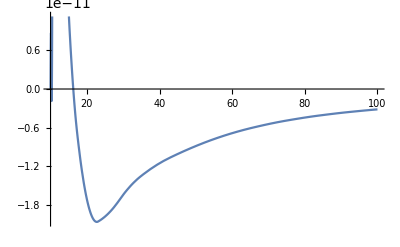
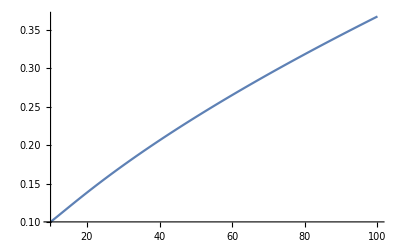
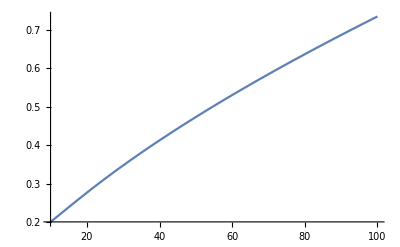
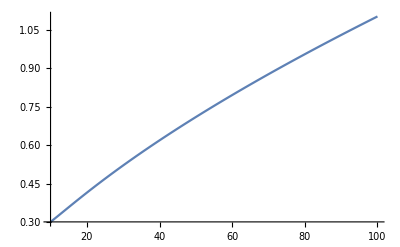
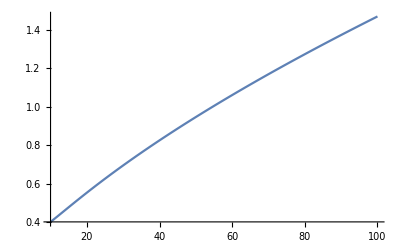
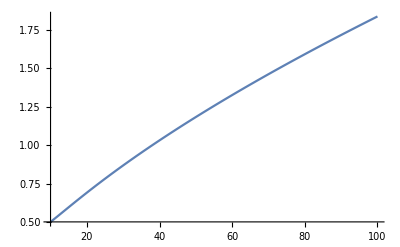
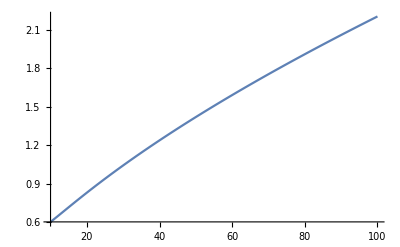
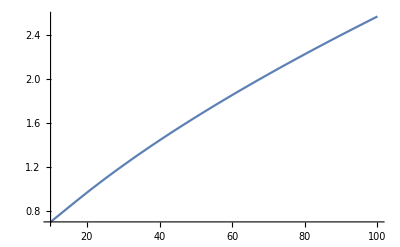

```mathematica
Table[Plot[u[x]/. soli,{x,10,100}],{soli,FirstTable}]
```

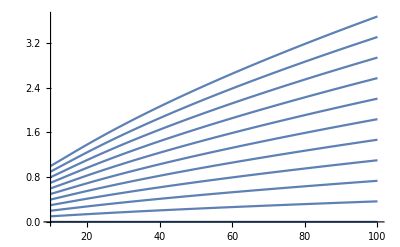

```mathematica
Plot[Table[u[x]/. soli,{soli,FirstTable}],{x,10,100},PlotRange->All]
```

### Square the constraint equation (which should have same result) and proceed with plots of u[x]

```mathematica
(* Try squaring eq 64 and/or Uconstraint to eliminate NDSolve complaints about the sqrt around the indefinite integral*)
UconstraintSquared=Simplify [0==((1-2M/x)^(3/2)(-1/(2x^2Sqrt[1-2M/x])Subscript[dϕ, 2][x]+D[dN[x]/Sqrt[1-2M/x]/. dNofx,x])^2)]
```

(20 x^6 (-2 M+x)^(3/2) (∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx)^2+4 c^2 (2 M-x)^5 x^(3/2) (e √x (-2 M+x) (28 M √(1-(2 M)/x)+(-1+3 √(1-(2 M)/x)) x)+3 c^2 (56 M^2+(-4+√(1-(2 M)/x)) x^2+√(1-(2 M)/x) x^(3/2) √(-2 M+x)+M (-20 x+2 √(1-(2 M)/x) √x √(-2 M+x)))) u[x]+16 √(1-(2 M)/x) (-2 M+x)^(21/2) u[x]^2+c^2 x^(5/2) (432 c^6 M^3 x-144 c^4 e M^3 √(1-(2 M)/x) x^(3/2)-432 c^6 M^2 x^2+156 c^4 e M^2 √(1-(2 M)/x) x^(5/2)+36 c^6 M x^3-12 c^4 e M √(1-(2 M)/x) x^(7/2)+36 c^6 x^4-15 c^4 e √(1-(2 M)/x) x^(9/2)+36 c^6 x^(7/2) √(-2 M+x)-10 c^2 e^2 M x^(7/2) √(-2 M+x)-27 c^4 e √(1-(2 M)/x) x^4 √(-2 M+x)+5 c^2 e^2 x^(9/2) √(-2 M+x)+16 (3 c^2-e √(1-(2 M)/x) √x) (-2 M+x)^7 u'[x])+(∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx) (20 c^2 e x^6 (-2 M+x)^(3/2)-6 c^4 √(1-(2 M)/x) x^4 (48 M^3-52 M^2 x+4 M x^2+5 x^3+9 x^(5/2) √(-2 M+x))-8 x^2 (-2 M+x)^6 (28 M √(1-(2 M)/x)+(-1+3 √(1-(2 M)/x)) x) u[x]-32 √(1-(2 M)/x) x^3 (-2 M+x)^7 u'[x]))^2/(256 c^2 √(1-(2 M)/x) x^14 (-2 M+x)^3 (-3 c^4+c^2 e √(1-(2 M)/x) √x+2 √(1-(2 M)/x) √x ∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx)^3)==0

### Simplify U(x) constraint equation

```mathematica
(* FullSimplify[UconstraintSquared] runs forever *)
(* DSolve[UconstraintSquared,{u[x]},{x}] runs forever *)
(* Simplify Numerator produces the same *)
(* FullSimplify Numerator may help. Simplify further manually. *) 
FullSimplify[(20 x^6 (-2 M+x)^(3/2) (∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx)^2+4 c^2 (2 M-x)^5 x^(3/2) (e √x (-2 M+x) (28 M √(1-(2 M)/x)+(-1+3 √(1-(2 M)/x)) x)+3 c^2 (56 M^2+(-4+√(1-(2 M)/x)) x^2+√(1-(2 M)/x) x^(3/2) √(-2 M+x)+M (-20 x+2 √(1-(2 M)/x) √x √(-2 M+x)))) u[x]+16 √(1-(2 M)/x) (-2 M+x)^(21/2) u[x]^2+c^2 x^(5/2) (432 c^6 M^3 x-144 c^4 e M^3 √(1-(2 M)/x) x^(3/2)-432 c^6 M^2 x^2+156 c^4 e M^2 √(1-(2 M)/x) x^(5/2)+36 c^6 M x^3-12 c^4 e M √(1-(2 M)/x) x^(7/2)+36 c^6 x^4-15 c^4 e √(1-(2 M)/x) x^(9/2)+36 c^6 x^(7/2) √(-2 M+x)-10 c^2 e^2 M x^(7/2) √(-2 M+x)-27 c^4 e √(1-(2 M)/x) x^4 √(-2 M+x)+5 c^2 e^2 x^(9/2) √(-2 M+x)+16 (3 c^2-e √(1-(2 M)/x) √x) (-2 M+x)^7 u'[x])+(∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx) (20 c^2 e x^6 (-2 M+x)^(3/2)-6 c^4 √(1-(2 M)/x) x^4 (48 M^3-52 M^2 x+4 M x^2+5 x^3+9 x^(5/2) √(-2 M+x))-8 x^2 (-2 M+x)^6 (28 M √(1-(2 M)/x)+(-1+3 √(1-(2 M)/x)) x) u[x]-32 √(1-(2 M)/x) x^3 (-2 M+x)^7 u'[x]))^2==0]
```

5 c^4 e^2 x^6 (-2 M+x)^(3/2)+36 c^8 x^(7/2) (12 M^3-12 M^2 x+M x^2+x^3+x^(5/2) √(-2 M+x))+20 x^6 (-2 M+x)^(3/2) (∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx)^2+4 (2 M-x)^5 (c^2 e x^2 (-2 M+x) (-x+√(1-(2 M)/x) (28 M+3 x)) u[x]+3 c^4 x^(3/2) (56 M^2+(-4+√(1-(2 M)/x)) x^2+√(1-(2 M)/x) x^(3/2) √(-2 M+x)+M (-20 x+2 √(1-(2 M)/x) √x √(-2 M+x))) u[x]-4 √(1-(2 M)/x) (-2 M+x)^(11/2) u[x]^2+4 c^2 (-3 c^2+e √(1-(2 M)/x) √x) x^(5/2) (-2 M+x)^2 u'[x])==3 c^6 e √(1-(2 M)/x) x^4 (48 M^3-52 M^2 x+4 M x^2+5 x^3+9 x^(5/2) √(-2 M+x))+2 x^2 (∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx) (-10 c^2 e x^4 (-2 M+x)^(3/2)+3 c^4 √(1-(2 M)/x) x^2 (48 M^3-52 M^2 x+4 M x^2+5 x^3+9 x^(5/2) √(-2 M+x))+4 (-2 M+x)^6 ((-x+√(1-(2 M)/x) (28 M+3 x)) u[x]+4 √(1-(2 M)/x) x (-2 M+x) u'[x]))

```mathematica
(* Define coefficients for terms with different powers, derivatives, and combinations of U(x) and the integral of U(x) *)
(* Integral of U(x) *)
Uintegral=∫((-2 M+x)^(7/2) u[x])/x^3 ⅆx;
(* No powers of U(x) *)
f1= 5 c^4 e^2 x^6 (-2 M+x)^(3/2)+36 c^8 x^(7/2) (12 M^3-12 M^2 x+M x^2+x^3+x^(5/2) √(-2 M+x))-(3 c^6 e √(1-(2 M)/x) x^4 (48 M^3-52 M^2 x+4 M x^2+5 x^3+9 x^(5/2) √(-2 M+x)))
(* Coefficient of U(x) *)
f2= 4 (2 M-x)^5 (c^2 e x^2 (-2 M+x) (-x+√(1-(2 M)/x) (28 M+3 x))+3 c^4 x^(3/2) (56 M^2+(-4+√(1-(2 M)/x)) x^2+√(1-(2 M)/x) x^(3/2) √(-2 M+x)+M (-20 x+2 √(1-(2 M)/x) √x √(-2 M+x))) )
(* Coefficient of U(x)^2 *)
f3=4 (2 M-x)^5 *(-4 √(1-(2 M)/x) (-2 M+x)^(11/2))
(* Coefficient of U'(x) *)
f4=4 (2 M-x)^5 (4 c^2 (-3 c^2+e √(1-(2 M)/x) √x) x^(5/2) (-2 M+x)^2 )
(* Coefficient of Integral of U(x) *)
f5= -2 x^2 (-10 c^2 e x^4 (-2 M+x)^(3/2)+3 c^4 √(1-(2 M)/x) x^2 (48 M^3-52 M^2 x+4 M x^2+5 x^3+9 x^(5/2) √(-2 M+x)))
(* Coefficient of U(x) times integral of U(x) *)
f6=- 2 x^2 4 (-2 M+x)^6 (-x+√(1-(2 M)/x) (28 M+3 x)) 
(* Coefficient of U'(x) times integral of Ux *)
f7=-2 x^2 4 (-2 M+x)^6 4 √(1-(2 M)/x) x (-2 M+x) 
(* Coefficient of integral of U(x) squared *)
f8=20 x^6 (-2 M+x)^(3/2)
```

5 c^4 e^2 x^6 (-2 M+x)^(3/2)+36 c^8 x^(7/2) (12 M^3-12 M^2 x+M x^2+x^3+x^(5/2) √(-2 M+x))-3 c^6 e √(1-(2 M)/x) x^4 (48 M^3-52 M^2 x+4 M x^2+5 x^3+9 x^(5/2) √(-2 M+x))

4 (2 M-x)^5 (c^2 e x^2 (-2 M+x) (-x+√(1-(2 M)/x) (28 M+3 x))+3 c^4 x^(3/2) (56 M^2+(-4+√(1-(2 M)/x)) x^2+√(1-(2 M)/x) x^(3/2) √(-2 M+x)+M (-20 x+2 √(1-(2 M)/x) √x √(-2 M+x))))

-16 √(1-(2 M)/x) (2 M-x)^5 (-2 M+x)^(11/2)

16 c^2 (-3 c^2+e √(1-(2 M)/x) √x) (2 M-x)^5 x^(5/2) (-2 M+x)^2

-2 x^2 (-10 c^2 e x^4 (-2 M+x)^(3/2)+3 c^4 √(1-(2 M)/x) x^2 (48 M^3-52 M^2 x+4 M x^2+5 x^3+9 x^(5/2) √(-2 M+x)))

-8 x^2 (-2 M+x)^6 (-x+√(1-(2 M)/x) (28 M+3 x))

-32 √(1-(2 M)/x) x^3 (-2 M+x)^7

20 x^6 (-2 M+x)^(3/2)

```mathematica
(* Simplification calculations *)
```

```mathematica
Factor[48a^3-52a^2b+4a b^2+5b^3]
```

(6 a-5 b) (2 a-b) (4 a+b)

```mathematica
Factor[12a^3-12a^2 b+a b^2+b^3]
```

(2 a-b) (6 a^2-3 a b-b^2)

```mathematica
(* Check Martin's f1 and f2 against mine *)
Mf1=36c^8Sqrt[1-2M/x]((1+Sqrt[1-2M/x](1+3M/x-6M^2/x^2))-3c^6e Sqrt[x](1-2M/x)^(3/2)(5+14M/x-24M^2/x^2+9Sqrt[1-2M/x])+5c^4e^2 x(1-2M/x)^(3/2));
Mf2=-12c^4x^2(1-2M/x)^(11/2)(Sqrt[1-2M/x](3+26M/x)-1)-4c^2e x^(5/2)(1-2M/x)^6((3+28M/x)Sqrt[1-2M/x]-1);
```

```mathematica
BooleanQ[f1=x^(13/2) Mf1]
BooleanQ[f2=-x^(13/2) Mf2]
```

False

False

```mathematica
BooleanQ[Sqrt[1-2/y](5+14/y-24/y^2)== (48/y^3-52/y^2+4/y+5)/Sqrt[1-2/y]]
```

False

### Create graphs for various ranges of x and for various initial conditions a

```mathematica
(* Define initial conditions and ranges *)
xi=2.5;
xf=5;
ui=0.01;
uf=.1;
ustep=.05;
xRange={x,xi,xf};
uValues=Table[uinitial,{uinitial, ui, uf, ustep}]
```

{0.01,0.06}

{{{u[x]→InterpolatingFunction[…][x]},{u[x]→InterpolatingFunction[…][x]}},{{u[x]→InterpolatingFunction[…][x]},{u[x]→InterpolatingFunction[…][x]}}}

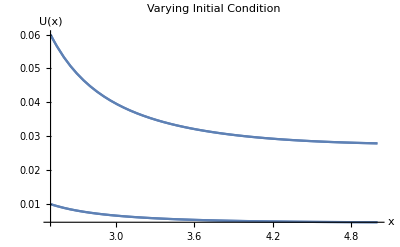

```mathematica
TestTable=Table[NDSolve[{UconstraintSquared/. constants, u[xi]==uinitial}, u[x], xRange],{uinitial,uValues}]
Plot[Table[u[x]/. soli,{soli,TestTable}],xRange,PlotRange->All, PlotLabel-> "Varying Initial Condition", AxesLabel->{"x","U(x)"}]
(* could add a , PlotLegends-> uValues for labels but not labeling the second correctly, similar to how it isn't making the second plot a different color *)
```

## Try to find a fit for u[x] which scales with initial condition

### Mathematica fitting tools

```mathematica
(* define table of data to fit *)
data=TestTable[[1]]
func=u[x]/.data
fittable=Table[{i,func[[1]]/. x->i}, {i,xi,xf, .1}]
```

{{u[x]→InterpolatingFunction[…][x]},{u[x]→InterpolatingFunction[…][x]}}

{InterpolatingFunction[…][x],InterpolatingFunction[…][x]}

{{2.5,0.01},{2.6,0.00890829},{2.7,0.00809879},{2.8,0.00748032},{2.9,0.00699611},{3.,0.00660935},{3.1,0.00629537},{3.2,0.00603701},{3.3,0.00582204},{3.4,0.00564151},{3.5,0.00548875},{3.6,0.00535869},{3.7,0.00524737},{3.8,0.00515171},{3.9,0.00506927},{4.,0.00499807},{4.1,0.00493649},{4.2,0.00488322},{4.3,0.00483715},{4.4,0.00479739},{4.5,0.00476316},{4.6,0.0047338},{4.7,0.00470876},{4.8,0.00468757},{4.9,0.00466982},{5.,0.00465514}}

```mathematica
(* Let Mathematica fit a hyperbola *)
cees=FindFit[fittable,c1/(x+c2)+c3,{c1,c2,c3},x]
```

{c1→0.00276518,c2→-2.07278,c3→0.00360876}

```mathematica
(* Let Mathematica fit a decaying exponential *)
bees=FindFit[fittable,b1 E^(-b2 x)+b3,{b1,b2,b3},x]
```

{b1→0.656569,b2→1.93694,b3→0.00467896}

### Graph and compare exponential fit(s) (not the best--skip)

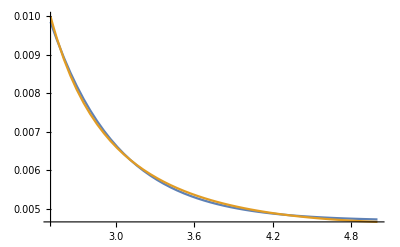

```mathematica
(* exponential fit *)
Plot[{(b1 E^(-b2 x)+b3)/.bees, func[[1]]}, {x,xi,xf}, PlotRange->All]
```

### Graph and compare hyperbolic fit(s) (best yet!)

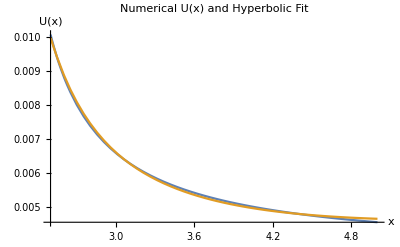

```mathematica
(* hyperbolic fit BEST YET *)
Plot[{(c1/(x+c2)+c3)/.cees, func[[1]]}, {x,xi,xf}, PlotRange->All, PlotLabel-> "Numerical U(x) and Hyperbolic Fit", AxesLabel->{"x","U(x)"}]
```

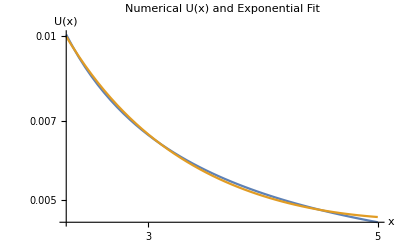

```mathematica
(* log-log plot to test the hyperbolic fit (not great at larger x) *)
LogLogPlot[{(c1/(x+c2)+c3)/.cees, func[[1]]}, {x,xi,xf}, PlotRange->All, PlotLabel-> "Numerical U(x) and Exponential Fit", AxesLabel->{"x","U(x)"}]
```

### Tuning a function manually (not necessary)

```mathematica
(* tune a decreasing exponential with a parameter for the initial condition u[10] *)
```

```mathematica
(* Removed one parameter using a point from the table as an initial condition constraint. *)
Manipulate[Plot[{(b1 E^(-b2 x)+2.5-b1 E^(-492 b2)), func[[1]]}, {x,2.5,10}, PlotRange->All], {b1, 5000,100000},{b2, 1,3}]
```